```mathematica
(*---------------------------------------------------*)
(* Q1 *)
(*---------------------------------------------------*)
f[x_]:=x Exp[-x]+x (1-x)
```

```mathematica
f[0]
```

0

```mathematica
f[0.1]
```

0.180484

```mathematica
f[0.2]
```

0.323746

```mathematica
f[0.4]
```

0.508128

```mathematica
f[0.8]
```

0.519463

```mathematica
(*---------------------------------------------------*)
(* Q2 *)
(*---------------------------------------------------*)
fB[x_] := BesselJ[1,x]
```

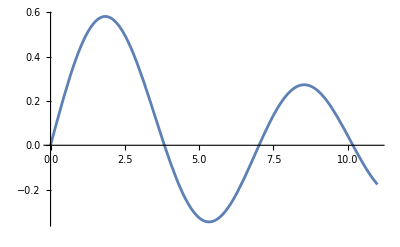

```mathematica
Plot[BesselJ[1,x], {x,0,11}]
```

```mathematica
FindRoot[BesselJ[1,x]== 0,{x,4}]
```

{2→3.83171}

```mathematica
FindRoot[BesselJ[1,x]== 0,{x,6}]
```

{2→7.01559}

```mathematica
FindRoot[BesselJ[1,x]== 0,{x,10}]
```

{2→10.1735}

```mathematica
(*---------------------------------------------------*)
```

```mathematica
(* Q3 *)
(*---------------------------------------------------*)
```

```mathematica
fI[x_] := Sin[x]*Exp[-x]
Clear[x]
```

```mathematica
integ = Integrate[fI[x],x]
```

```mathematica
-1/2 ⅇ^-x (Cos[x]+Sin[x])
D[integ,x]
```

-1/2 ⅇ^-x (Cos[x]+Sin[x])

```mathematica
(*---------------------------------------------------*)
```

```mathematica
(* Q4 *)
(*---------------------------------------------------*)
fS[x_]:= Exp[-ArcTan[x]]
ser = Series[fS[x],{x,0,5}]
```

1-x+x^2/2+x^3/6-(7 x^4)/24-x^5/24+O[x]^6

```mathematica
serInf = Series[fS[x], {x,Infinity,5}]
```

ⅇ^(-π/2)+ⅇ^(-π/2)/x+ⅇ^(-π/2)/(2 x^2)-ⅇ^(-π/2)/(6 x^3)-(7 ⅇ^(-π/2))/(24 x^4)+ⅇ^(-π/2)/(24 x^5)+O[1/x]^6

```mathematica
(*---------------------------------------------------*)
(* Q5 *)
(*---------------------------------------------------*)
```

```mathematica
(*a*)
dsol = DSolve[{z''[x]-x*z[x]==0, z[0]==1,z'[0]==-3^(1/3) Gamma[2/3]/Gamma[1/3]},z[x],x]
```

{{z[x]→3^(2/3) AiryAi[x] Gamma[2/3]}}

```mathematica
ysol = z[x] /.Flatten[dsol]

ndsol = NDSolve[{y''[x]-x*y[x]==0, y[0]==1,y'[0]==-3^(1/3) Gamma[2/3]/Gamma[1/3]}, y[x],{x,-10,10}]
```

3^(2/3) AiryAi[x] Gamma[2/3]

{{y[x]→InterpolatingFunction[…][x]}}

```mathematica
yndsol=y[x]/.Flatten[ndsol]
```

InterpolatingFunction[…][x]

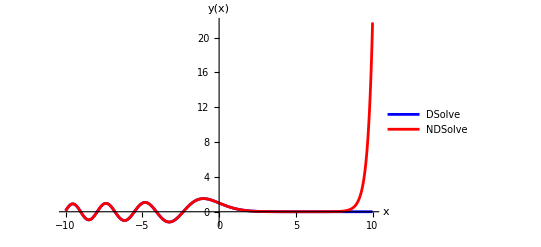

PropertyList::pvobj: y is not an object with properties.

Integrate::ilim: Invalid integration variable or limit(s) in 2.

D::ivar: 2 is not a valid variable.

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Solve::ivar: 2 is not a valid variable.

```mathematica
Plot[{ysol,yndsol},{x,-10,10},PlotLegends->{"DSolve","NDSolve"},PlotRange->All,AxesLabel->{"x","y(x)"},PlotStyle->{Blue,Red}]
```